# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-24

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-10,13},{2022-01-11,39},{2022-01-12,38},{2022-01-13,30},{2022-01-14,12},{2022-01-15,11},{2022-01-16,9},{2022-01-17,5},{2022-01-18,4},{2022-01-19,1},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Arizona→{{2022-01-10,562},{2022-01-11,513},{2022-01-12,566},{2022-01-13,380},{2022-01-14,365},{2022-01-15,226},{2022-01-16,371},{2022-01-17,265},{2022-01-18,244},{2022-01-19,361},{2022-01-20,77},{2022-01-21,76},{2022-01-22,138},{2022-01-23,141},{2022-01-24,471}},Arkansas→{{2022-01-10,200},{2022-01-11,198},{2022-01-12,173},{2022-01-13,92},{2022-01-14,152},{2022-01-15,13},{2022-01-16,15},{2022-01-17,6},{2022-01-18,49},{2022-01-19,26},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},California→{{2022-01-10,476},{2022-01-11,332},{2022-01-12,339},{2022-01-13,200},{2022-01-14,343},{2022-01-15,677},{2022-01-16,960},{2022-01-17,1844},{2022-01-18,879},{2022-01-19,117},{2022-01-20,42},{2022-01-21,164},{2022-01-22,890},{2022-01-23,83},{2022-01-24,156}},Colorado→{{2022-01-10,800},{2022-01-11,470},{2022-01-12,803},{2022-01-13,162},{2022-01-14,256},{2022-01-15,311},{2022-01-16,392},{2022-01-17,76},{2022-01-18,226},{2022-01-19,223},{2022-01-20,61},{2022-01-21,73},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Connecticut→{{2022-01-10,99},{2022-01-11,85},{2022-01-12,92},{2022-01-13,47},{2022-01-14,125},{2022-01-15,65},{2022-01-16,74},{2022-01-17,49},{2022-01-18,90},{2022-01-19,104},{2022-01-20,103},{2022-01-21,163},{2022-01-22,16},{2022-01-23,35},{2022-01-24,30}},Delaware→{{2022-01-10,66},{2022-01-11,67},{2022-01-12,36},{2022-01-13,33},{2022-01-14,57},{2022-01-15,33},{2022-01-16,25},{2022-01-17,44},{2022-01-18,62},{2022-01-19,31},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Florida→{{2022-01-10,276},{2022-01-11,225},{2022-01-12,156},{2022-01-13,111},{2022-01-14,51},{2022-01-15,94},{2022-01-16,92},{2022-01-17,57},{2022-01-18,65},{2022-01-19,33},{2022-01-20,0},{2022-01-21,15},{2022-01-22,14},{2022-01-23,14},{2022-01-24,14}},Georgia→{{2022-01-10,146},{2022-01-11,138},{2022-01-12,118},{2022-01-13,105},{2022-01-14,79},{2022-01-15,35},{2022-01-16,50},{2022-01-17,115},{2022-01-18,351},{2022-01-19,230},{2022-01-20,37},{2022-01-21,43},{2022-01-22,5},{2022-01-23,6},{2022-01-24,1}},Illinois→{{2022-01-10,178},{2022-01-11,137},{2022-01-12,59},{2022-01-13,64},{2022-01-14,37},{2022-01-15,14},{2022-01-16,31},{2022-01-17,56},{2022-01-18,124},{2022-01-19,93},{2022-01-20,20},{2022-01-21,0},{2022-01-22,0},{2022-01-23,2},{2022-01-24,1}},Indiana→{{2022-01-10,99},{2022-01-11,132},{2022-01-12,117},{2022-01-13,121},{2022-01-14,26},{2022-01-15,31},{2022-01-16,27},{2022-01-17,31},{2022-01-18,24},{2022-01-19,33},{2022-01-20,60},{2022-01-21,164},{2022-01-22,2},{2022-01-23,1},{2022-01-24,15}},Louisiana→{{2022-01-10,48},{2022-01-11,19},{2022-01-12,51},{2022-01-13,50},{2022-01-14,26},{2022-01-15,37},{2022-01-16,16},{2022-01-17,15},{2022-01-18,48},{2022-01-19,47},{2022-01-20,22},{2022-01-21,56},{2022-01-22,0},{2022-01-23,0},{2022-01-24,29}},Maryland→{{2022-01-10,166},{2022-01-11,229},{2022-01-12,178},{2022-01-13,125},{2022-01-14,67},{2022-01-15,50},{2022-01-16,48},{2022-01-17,49},{2022-01-18,101},{2022-01-19,68},{2022-01-20,12},{2022-01-21,9},{2022-01-22,5},{2022-01-23,3},{2022-01-24,4}},Massachusetts→{{2022-01-10,1185},{2022-01-11,786},{2022-01-12,800},{2022-01-13,698},{2022-01-14,1029},{2022-01-15,367},{2022-01-16,362},{2022-01-17,812},{2022-01-18,741},{2022-01-19,684},{2022-01-20,741},{2022-01-21,250},{2022-01-22,225},{2022-01-23,412},{2022-01-24,128}},Michigan→{{2022-01-10,175},{2022-01-11,79},{2022-01-12,108},{2022-01-13,86},{2022-01-14,66},{2022-01-15,21},{2022-01-16,29},{2022-01-17,24},{2022-01-18,4},{2022-01-19,4},{2022-01-20,1},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Minnesota→{{2022-01-10,159},{2022-01-11,684},{2022-01-12,345},{2022-01-13,148},{2022-01-14,96},{2022-01-15,29},{2022-01-16,48},{2022-01-17,71},{2022-01-18,386},{2022-01-19,71},{2022-01-20,55},{2022-01-21,35},{2022-01-22,125},{2022-01-23,24},{2022-01-24,29}},Nebraska→{{2022-01-10,78},{2022-01-11,77},{2022-01-12,97},{2022-01-13,115},{2022-01-14,44},{2022-01-15,27},{2022-01-16,48},{2022-01-17,53},{2022-01-18,107},{2022-01-19,50},{2022-01-20,81},{2022-01-21,68},{2022-01-22,42},{2022-01-23,4},{2022-01-24,81}},Nevada→{{2022-01-10,149},{2022-01-11,115},{2022-01-12,68},{2022-01-13,74},{2022-01-14,28},{2022-01-15,4},{2022-01-16,3},{2022-01-17,21},{2022-01-18,20},{2022-01-19,38},{2022-01-20,23},{2022-01-21,2},{2022-01-22,2},{2022-01-23,0},{2022-01-24,28}},New Hampshire→{{2022-01-10,37},{2022-01-11,28},{2022-01-12,19},{2022-01-13,45},{2022-01-14,87},{2022-01-15,35},{2022-01-16,40},{2022-01-17,20},{2022-01-18,32},{2022-01-19,21},{2022-01-20,27},{2022-01-21,3},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},New Jersey→{{2022-01-10,206},{2022-01-11,552},{2022-01-12,505},{2022-01-13,125},{2022-01-14,181},{2022-01-15,21},{2022-01-16,27},{2022-01-17,70},{2022-01-18,73},{2022-01-19,215},{2022-01-20,1},{2022-01-21,0},{2022-01-22,1},{2022-01-23,0},{2022-01-24,1}},New Mexico→{{2022-01-10,108},{2022-01-11,117},{2022-01-12,145},{2022-01-13,53},{2022-01-14,55},{2022-01-15,15},{2022-01-16,3},{2022-01-17,11},{2022-01-18,16},{2022-01-19,2},{2022-01-20,0},{2022-01-21,1},{2022-01-22,1},{2022-01-23,0},{2022-01-24,0}},New York→{{2022-01-10,866},{2022-01-11,899},{2022-01-12,792},{2022-01-13,684},{2022-01-14,595},{2022-01-15,390},{2022-01-16,180},{2022-01-17,135},{2022-01-18,313},{2022-01-19,209},{2022-01-20,48},{2022-01-21,29},{2022-01-22,15},{2022-01-23,21},{2022-01-24,42}},North Carolina→{{2022-01-10,322},{2022-01-11,239},{2022-01-12,138},{2022-01-13,92},{2022-01-14,130},{2022-01-15,114},{2022-01-16,48},{2022-01-17,139},{2022-01-18,414},{2022-01-19,280},{2022-01-20,42},{2022-01-21,47},{2022-01-22,80},{2022-01-23,92},{2022-01-24,76}},North Dakota→{{2022-01-10,29},{2022-01-11,137},{2022-01-12,46},{2022-01-13,42},{2022-01-14,53},{2022-01-15,124},{2022-01-16,32},{2022-01-17,41},{2022-01-18,136},{2022-01-19,51},{2022-01-20,78},{2022-01-21,94},{2022-01-22,52},{2022-01-23,12},{2022-01-24,81}},Ohio→{{2022-01-10,139},{2022-01-11,141},{2022-01-12,112},{2022-01-13,206},{2022-01-14,85},{2022-01-15,9},{2022-01-16,15},{2022-01-17,7},{2022-01-18,109},{2022-01-19,73},{2022-01-20,80},{2022-01-21,105},{2022-01-22,1},{2022-01-23,0},{2022-01-24,87}},Oregon→{{2022-01-10,232},{2022-01-11,353},{2022-01-12,291},{2022-01-13,226},{2022-01-14,174},{2022-01-15,21},{2022-01-16,32},{2022-01-17,59},{2022-01-18,219},{2022-01-19,63},{2022-01-20,25},{2022-01-21,10},{2022-01-22,0},{2022-01-23,2},{2022-01-24,11}},Pennsylvania→{{2022-01-10,61},{2022-01-11,211},{2022-01-12,158},{2022-01-13,40},{2022-01-14,20},{2022-01-15,50},{2022-01-16,22},{2022-01-17,7},{2022-01-18,44},{2022-01-19,156},{2022-01-20,6},{2022-01-21,36},{2022-01-22,14},{2022-01-23,0},{2022-01-24,6}},South Carolina→{{2022-01-10,67},{2022-01-11,91},{2022-01-12,54},{2022-01-13,35},{2022-01-14,4},{2022-01-15,5},{2022-01-16,6},{2022-01-17,37},{2022-01-18,137},{2022-01-19,57},{2022-01-20,1},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Tennessee→{{2022-01-10,62},{2022-01-11,46},{2022-01-12,54},{2022-01-13,48},{2022-01-14,69},{2022-01-15,18},{2022-01-16,14},{2022-01-17,4},{2022-01-18,13},{2022-01-19,23},{2022-01-20,4},{2022-01-21,2},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Texas→{{2022-01-10,224},{2022-01-11,226},{2022-01-12,112},{2022-01-13,178},{2022-01-14,977},{2022-01-15,603},{2022-01-16,350},{2022-01-17,41},{2022-01-18,64},{2022-01-19,93},{2022-01-20,206},{2022-01-21,342},{2022-01-22,141},{2022-01-23,0},{2022-01-24,0}},Utah→{{2022-01-10,464},{2022-01-11,388},{2022-01-12,356},{2022-01-13,182},{2022-01-14,216},{2022-01-15,214},{2022-01-16,19},{2022-01-17,376},{2022-01-18,372},{2022-01-19,262},{2022-01-20,38},{2022-01-21,0},{2022-01-22,0},{2022-01-23,1},{2022-01-24,0}},Vermont→{{2022-01-10,30},{2022-01-11,479},{2022-01-12,94},{2022-01-13,69},{2022-01-14,201},{2022-01-15,91},{2022-01-16,47},{2022-01-17,178},{2022-01-18,249},{2022-01-19,140},{2022-01-20,117},{2022-01-21,24},{2022-01-22,12},{2022-01-23,0},{2022-01-24,0}},Virginia→{{2022-01-10,184},{2022-01-11,114},{2022-01-12,34},{2022-01-13,15},{2022-01-14,13},{2022-01-15,3},{2022-01-16,3},{2022-01-17,9},{2022-01-18,241},{2022-01-19,40},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0}},Washington→{{2022-01-10,743},{2022-01-11,312},{2022-01-12,240},{2022-01-13,266},{2022-01-14,157},{2022-01-15,17},{2022-01-16,25},{2022-01-17,112},{2022-01-18,340},{2022-01-19,162},{2022-01-20,69},{2022-01-21,55},{2022-01-22,1},{2022-01-23,3},{2022-01-24,75}},Wisconsin→{{2022-01-10,183},{2022-01-11,77},{2022-01-12,90},{2022-01-13,104},{2022-01-14,199},{2022-01-15,59},{2022-01-16,52},{2022-01-17,78},{2022-01-18,52},{2022-01-19,59},{2022-01-20,34},{2022-01-21,47},{2022-01-22,17},{2022-01-23,0},{2022-01-24,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

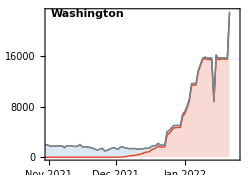

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

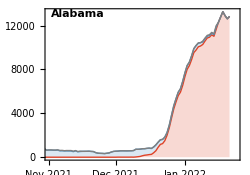
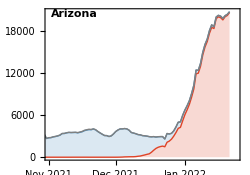
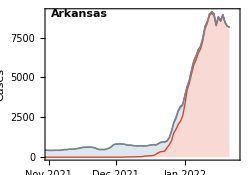
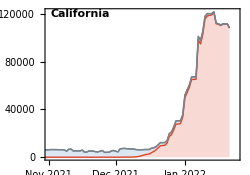
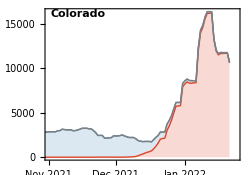
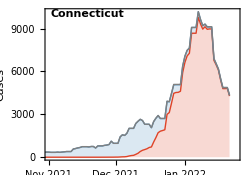
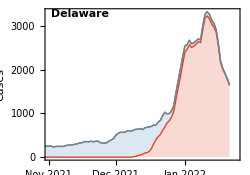
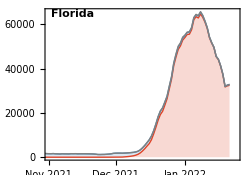
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png